```mathematica
SetDirectory["/home/czhou/Projects/InvEHL/resources"];
```

```mathematica
Dimensions@xy
```

{16800,2}

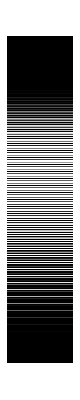

```mathematica
ArrayPlot@Import["./abc.txt","Table"]
```

```mathematica
z=Flatten[Import["./c.txt","Table"],1];
xy=Import["./mesh/node.txt","Table"];
Table[{xy⟦i,1⟧,xy⟦i,2⟧,z⟦i⟧},{i,1,Length@z}];
ListPlot3D[%,PlotRange->All,BoxRatios->{1,1,0.5},InterpolationOrder->1]
```

-Graphics3D-

```mathematica
"
```

```mathematica
(*
Import["./cat.jpg"];
ImageTake[%,20{1,-1},{1,-1}]
ImagePad[%,{{-10,-10},{-1-10,-1+10}},1]
Export["cat.jpg",%]*)
```

-Graphics-

```mathematica
-Graphics-//std::cout <<b.size();
```

cat.jpg

```mathematica
o0=ListContourPlot[(ImageData@ImageResize[Import["images/heart.png"],{200,200}])⟦All,All,1⟧,ImageSize->500,PlotRange->All,Contours->10,PerformanceGoal->"Quality"]
```

-Graphics-

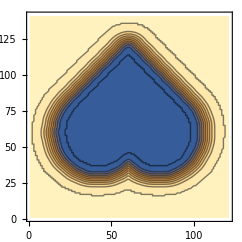

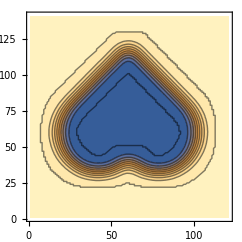

```mathematica
min=0.000;
max=1;
imgSize=2*121;
ct=Range[min,max,(max-min)/10];
img=Import["output_ls.png"];Dimensions@ImageData@img;
o1=ListContourPlot[(ImageData@Import["output_ls.png"])⟦All,All⟧,ImageSize->imgSize,PlotRange->All,Contours->ct,PerformanceGoal->"Quality"]
img=Import["output_gf.png"];Dimensions@ImageData@img;
o2=ListContourPlot[(ImageData@img)⟦All,All⟧,ImageSize->imgSize,PlotRange->All,Contours->ct,PerformanceGoal->"Quality"]
```

```mathematica
ListPlot3D[ImageData@Import["output_gf.png"],BoxRatios->{1, 1, 0.2},
PerformanceGoal->"Quality",ImageSize->1000,PlotRange->All]
```

-Graphics3D-